### Haldane model

```mathematica
a0={0,0};a1={(√3)/2,1/2};a2={0,1};
σ0={{1,0},{0,1}};σx={{0,1},{1,0}};σy={{0,-ⅈ},{ⅈ,0}};σz={{1,0},{0,-1}};
```

```mathematica
H[k1_,k2_]=t1( (1+Cos[2π k1]+Cos[2π k2])σx+(Sin[2π k1]+Sin[2π k2])σy)
+2t2 (Cos[ϕ](Cos[2π k1]+Cos[2π k2]+Cos[2π (k1-k2)])σ0+Sin[ϕ](Sin[2π k1]-Sin[2π k2]-Sin[2π (k1-k2)])σz);
```

{{0,t1 (1+Cos[2 k1 π]+Cos[2 k2 π]-ⅈ (Sin[2 k1 π]+Sin[2 k2 π]))},{t1 (1+Cos[2 k1 π]+Cos[2 k2 π]+ⅈ (Sin[2 k1 π]+Sin[2 k2 π])),0}}

```mathematica
energies[k1_,k2_]=Eigenvalues[H[k1,k2]]
```

{-t1 √(3+2 Cos[2 k1 π]+2 Cos[2 k2 π]+2 Cos[2 k1 π-2 k2 π]),t1 √(3+2 Cos[2 k1 π]+2 Cos[2 k2 π]+2 Cos[2 k1 π-2 k2 π])}

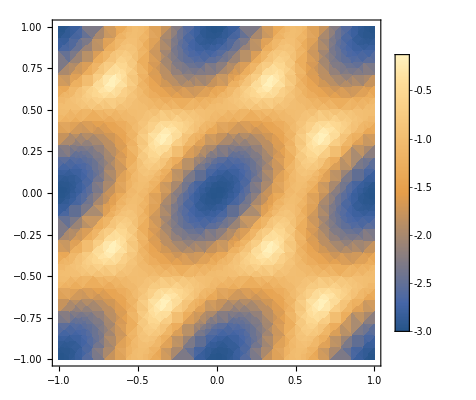

```mathematica
DensityPlot[energies[k1,k2][[1]]/.{t1->1,t2->0.2,ϕ->π/2},{k1,-1,1},{k2,-1,1},AspectRatio->1,PlotLegends->Automatic]
```

```mathematica
Plot3D[{energies[k1,k2][[1]],energies[k1,k2][[2]]}/.{t1->1,t2->0.2,ϕ->π/2},{k1,-1,1},{k2,-1,1},AspectRatio->1]
```

-Graphics3D-

```mathematica
{energies[1/3,-1/3][[1]],energies[1/3,-1/3][[2]]}/.{t1->1,t2->0.0,ϕ->π/2}
```

{0,0}

### Hofstadter Plot

```mathematica
t1=1;t2=3;ϕ0=π/2;
hofstadter[p_,q_,k1_,k2_]:=Module[{vals1A,vals1B,vals2A,vals2B,H1,H2,energies,M},
H1=Table[0,{n1,1,4q},{n2,1,4q}];
For[n1=1,n1≤2q,n1++,
H1[[{2n1-1,2n1},{2n1-1,2n1}]]={{0,Exp[-ⅈ π p/q *(n1+1/2)]+Exp[-ⅈ 2π k2]Exp[ⅈ π p/q *(n1+1/2)]},{Exp[ⅈ π p/q *(n1+1/2)]+Exp[ⅈ 2π k2]Exp[-ⅈ π p/q *(n1+1/2)],0}};
If[n1-1≥1,
H1[[{2n1-1,2n1},{2(n1-1)-1,2(n1-1)}]]={{0,0},{1,0}},
H1[[{2n1-1,2n1},{4q-1,4q}]]={{0,0},{1,0}}*Exp[-ⅈ 2π k1]
];
If[n1+1≤2q,
H1[[{2n1-1,2n1},{2(n1+1)-1,2(n1+1)}]]={{0,1},{0,0}},
H1[[{2n1-1,2n1},{1,2}]]={{0,1},{0,0}}*Exp[ⅈ 2π k1]
]];
H2 =Table[0,{n1,1,4q},{n2,1,4q}];
For[n1=1,n1≤2q,n1++,
vals2A=Exp[ⅈ ϕ0]Exp[-ⅈ 2π p/q *(n1+1/3)]Exp[ⅈ 2π k2];
vals2B=Exp[-ⅈ ϕ0]Exp[-ⅈ 2π p/q *(n1+2/3)]Exp[ⅈ 2π k2];
H2[[{2n1-1,2n1},{2n1-1,2n1}]]+={{vals2A,0},{0,vals2B}};
vals1A= (Exp[-ⅈ ϕ0]Exp[-ⅈ π p/q *(n1+5/6)]+Exp[ⅈ ϕ0]Exp[ⅈ π p/q *(n1+5/6)]Exp[-ⅈ 2π k2])*If[n1+1<=2q,1,Exp[ⅈ 2π k1]];
vals1B= (Exp[ⅈ ϕ0]Exp[-ⅈ π p/q *(n1+7/6)]+Exp[-ⅈ ϕ0]Exp[ⅈ π p/q *(n1+7/6)]Exp[-ⅈ 2π k2])*If[n1+1<=2q,1,Exp[ⅈ 2π k1]];
H2[[{2n1-1,2n1},If[n1+1<=2q,{2(n1+1)-1,2(n1+1)},{1,2}]]]+={{vals1A,0},{0,vals1B}}
];
energies = Eigenvalues[t1*H1+t2*(H2+ConjugateTranspose[H2])];
M= Sum[Sort[energies][[i]],{i,2q+p,4q}];
Print[p/q," ",M];
Thread[{Table[p/q,{i,1,4q}],energies}];
]
```

```mathematica
p1=ListPlot[Table[hofstadter[i,100,0.,0.],{i,1,99}],PlotStyle->Blue,AspectRatio->0.7,ImageSize->Large]
```

1/100 1274.6

1/50 1273.

3/100 1271.11

1/25 1269.01

1/20 1266.97

3/50 1264.84

7/100 1262.92

2/25 1261.

9/100 1259.45

1/10 1258.95

11/100 1256.79

3/25 1255.77

13/100 1255.96

7/50 1255.35

3/20 1253.31

4/25 1252.3

17/100 1253.51

9/50 1256.55

19/100 1257.9

1/5 1243.38

21/100 1260.58

11/50 1260.97

23/100 1258.33

6/25 1254.53

1/4 1264.53

13/50 1257.33

27/100 1262.71

7/25 1267.55

29/100 1270.61

3/10 1274.74

31/100 1278.51

8/25 1282.89

33/100 1287.45

17/50 1293.08

7/20 1299.54

9/25 1306.7

37/100 1314.06

19/50 1322.27

39/100 1331.6

2/5 1339.06

41/100 1331.24

21/50 1318.33

43/100 1306.99

11/25 1296.53

9/20 1287.3

23/50 1279.85

47/100 1271.65

12/25 1263.78

49/100 1255.88

1/2 1320.28

51/100 1243.2

13/25 1237.94

53/100 1233.48

27/50 1230.09

11/20 1226.37

14/25 1223.87

57/100 1224.31

29/50 1222.41

59/100 1221.43

3/5 1214.14

61/100 1222.68

31/50 1223.66

63/100 1224.91

16/25 1226.37

13/20 1229.06

33/50 1232.53

67/100 1225.36

17/25 1211.93

69/100 1198.13

7/10 1184.37

71/100 1170.71

18/25 1157.07

73/100 1144.95

37/50 1134.68

3/4 1122.26

19/25 1117.17

77/100 1110.14

39/50 1105.02

79/100 1102.48

4/5 1099.93

81/100 1095.95

41/50 1092.28

83/100 1089.42

21/25 1088.21

17/20 1088.87

43/50 1085.71

87/100 1076.35

22/25 1070.33

89/100 1067.03

9/10 1062.84

91/100 1060.14

23/25 1053.49

93/100 1049.4

47/50 1044.89

19/20 1040.27

24/25 1035.5

97/100 1030.67

49/50 1025.53

99/100 1020.36

-Graphics-

```mathematica
Sum[Table[]]
```